```mathematica
Quit[]; ClearAll
```

# 2 champs couplés

### Initialisation

```mathematica
Needs["PlotLegends`"];
```

```mathematica
(*
SetConst:=Block[{},amp1=1;amp2=2;ga=0.2;eps1=1000;eps2=2;C1=100/ga^2;];
*)
SetConst:=Block[{},amp1=1;amp2=3/2;ga=1/10;eps1=1/10;eps2=1/10;C1=100/ga^2;];
SetConst:=Block[{},amp1=Aamp1;amp2=Aamp2;ga=Aga;eps1=Aeps1;eps2=Aeps2;C1=AC1;C2=AC2;];
SetParameters[vamp1_,vamp2_,vga_,veps1_,veps2_,vC1_,vC2_]:=Block[{},Clear[Vnum];
Aamp1=vamp1;Aamp2=vamp2;Aga=vga;Aeps1=veps1;Aeps2=veps2;AC1=vC1;AC2=vC2;
SetConst;
];
UnSetConst:=Block[{},Clear[amp1,amp2,ga,eps1,eps2,C1,C2]];
HeureDExécution:=Print["Exécuté le: "<>DateString[Date[],{"DayShort"," ","MonthName",", ","Year"," - ","Hour12Short",":","Minute"," ","AMPMLowerCase"}]];
V1[f1_,f2_]:=(f1^2-amp1)^2(f1^2-eps1); 
(* V1[f1_,f2_]:=C1 f1^2(f1^2-amp1^2)^2 + eps1 f1^2; *)
(* V2[f1_,f2_]:=((f2^2-amp2)^2+eps2 f2)/(f1^2+ga); *)
V2[f1_,f2_]:=C1((f2^2-amp2^2)^2-eps2/4 (f2-2amp2)(f2+amp2)^2)/(f1^2+ga);
V[f1_,f2_]:=V1[f1,f2]+V2[f1,f2];
UnSetConst;
sub={amp1->Subscript[a, 1],amp2->Subscript[a, 2],ga->γ,eps1->Subscript[δ, 1],eps2->Subscript[δ, 2],C1->α,C2->β};
ShowPotential:=Block[{},
SetConst;
Vnum[f1_,f2_]=V[ψ,ϕ];
UnSetConst;
Print["Potentiel: V[ψ,ϕ] = ",V[ψ,ϕ]/.sub," = ",Vnum[ψ,ϕ]];
];
```

```mathematica
RechercheDesExtrema:=Block[{},UnSetConst;
Print["Recherche des extrema de V[ψ,ϕ] "];
Vp1[f1_,f2_]=D[V[f1,f2],f1];
Vp2[f1_,f2_]=D[V[f1,f2],f2];
Vp1p1[f1_,f2_]=D[D[V[f1,f2],f1],f1];
Vp1p2[f1_,f2_]=D[D[V[f1,f2],f1],f2];
Vp2p2[f1_,f2_]=D[D[V[f1,f2],f2],f2];
eqn1[f1_,f2_]:=-D[f1,{x,2}]+Vp1[f1,f2];
eqn2[f1_,f2_]:=-C1/C2 D[f2,{x,2}]+Vp2[f1,f2];
(* Print["Potential: V[ψ,ϕ]== ",V[ψ,ϕ]/.sub]; *)
Print["Equation for ψ: 0 == ",eqn1[ψ[x],ϕ[x]]/.sub];
Print["Equation for ϕ: 0 == ",eqn2[ψ[x],ϕ[x]]/.sub];
SetConst;

SetConst;
(* Print["Potentiel ",V[ψ,ϕ]]; *)
mmax=15;
xx0=Table[i,{i,-mmax,mmax}];
yy0=Table[j,{j,-mmax,mmax}];
xy=Table[{i,j},{i,-mmax,mmax},{j,-mmax,mmax}];
prec=12;
(*
MMIN=Chop[Table[FindMinimum[V[x,y],{x,1.0ii},{y,1.0jj},WorkingPrecision->60],{ii,-mmax,mmax},{jj,-mmax,mmax}]]//Quiet;
prec=12;TMMIN=Union[1./10^prec Round[10^prec Transpose[{Transpose[Flatten[MMIN,1]][[1]],x/.Transpose[Flatten[MMIN,1]][[2]],y/.Transpose[Flatten[MMIN,1]][[2]]}]]]; 
*)
Clear[MinMaxSelle];
MinMaxSelle:=If[Vp1p1[x,y]Vp2p2[x,y]⩾0,If[Vp1p1[x,y]⩾0,"minimum","maximum"],"selle"]/.solext;solext=NSolve[{Vp1[x,y]==0,Vp2[x,y]==0,x∈Reals&&y∈Reals},{x,y}];
MMIN3=Chop[{V[x,y],x,y,Vp1[x,y],Vp2[x,y],Vp1p1[x,y],Vp1p2[x,y],Vp2p2[x,y]}/.solext];
TMMIN3=Sort[Transpose[Append[Transpose[Chop[{V[x,y],x,y,(*Vp1[x,y],Vp2[x,y],*)Vp1p1[x,y],Vp1p2[x,y],Vp2p2[x,y]}/.solext]],MinMaxSelle]],#1[[1]]<#2[[1]]&];
TMMIN=TMMIN3;
TT=TMMIN3;
VV=Transpose[{Transpose[TT][[1]],Transpose[TT][[2]],Transpose[TT][[3]],Transpose[TT][[4]],Transpose[TT][[5]],Transpose[TT][[6]],Transpose[TT][[7]]}];
VVmin=VV;
Print["Position des minima de V[ψ,ϕ] : "];
VVno=Transpose[Prepend[Transpose[VV],Table[i,{i,1,Dimensions[TT][[1]]}]]];
VVnol={"Extremum","V","ψ","ϕ","∂^2 V/∂ψ^2","∂^2 V/∂ψ∂ϕ","∂^2 V/∂ϕ^2","Type"};
VVnoTable=Prepend[VVno,VVnol];
Print[VVnoTable//TableForm];


(*
MM={};
For[i=0,i<2mmax+1,For[j=0,j<2mmax+1,
xs=1.0 xx0[[i]];ys=1.0 yy0[[i]];
MM=Append[MM,Chop[FindMinimum[V[x,y],{x,xs},{y,ys},WorkingPrecision->60]//Quiet]];
,j++];,i++];
MMIN2=MM;
TMMIN2=Union[Transpose[1./10^prec Round[10^prec{Transpose[MMIN2][[1]],x/.Transpose[MMIN2][[2]],y/.Transpose[MMIN2][[2]]}]]];
(* TMMIN=TMMIN2; *)

TMMIN=TMMIN2;
MMIN=MMIN2;

TT=TMMIN;
Vpp11:=Apply[Vp1p1,Transpose[Drop[Transpose[TT],1]],1];
Vpp12:=Apply[Vp1p2,Transpose[Drop[Transpose[TT],1]],1];
Vpp22:=Apply[Vp2p2,Transpose[Drop[Transpose[TT],1]],1];VV=Transpose[{Transpose[TT][[1]],Transpose[TT][[2]],Transpose[TT][[3]],Vpp11,Vpp12,Vpp22}];
VVmin=VV;

Print["Position des minima de V[ψ,ϕ] : "];
(*Print[Prepend[TMMIN,{"V","ψ","ϕ"}]//TableForm];*)
(*Print[Prepend[VV,{"V","ψ","ϕ","∂^2/(∂ψ ∂ψ)","∂^2/(∂ψ ∂ϕ)","∂^2/(∂ϕ ∂ϕ)"}]//TableForm];*)
VVno=Transpose[Prepend[Transpose[VV],Table[i,{i,1,Dimensions[TT][[1]]}]]];
VVnol={"Min no.","V","ψ","ϕ","∂^2/(∂ψ ∂ψ)","∂^2/(∂ψ ∂ϕ)","∂^2/(∂ϕ ∂ϕ)"};
Print[Prepend[VVno,VVnol]//TableForm];

(* recherche des maxima relatifs *)
MM={};
For[i=0,i<2mmax+1,For[j=0,j<2mmax+1,
xs=1.0 xx0[[i]];ys=1.0 yy0[[i]];
MM=Append[MM,Chop[FindMaximum[V[x,y],{x,xs},{y,ys},WorkingPrecision->60]//Quiet]];
,j++];,i++];
MMIN2=MM;
TMMIN2=Union[Transpose[1./10^prec Round[10^prec{Transpose[MMIN2][[1]],x/.Transpose[MMIN2][[2]],y/.Transpose[MMIN2][[2]]}]]];
(* TMMIN=TMMIN2; *)
TMMAX=TMMIN2;
MMAX=MMIN2;

TT=TMMAX;
delmax={};
For[ii=0,ii<Dimensions[TT][[1]],
(* Print[Transpose[TT][[2]][[ii]]^2+Transpose[TT][[3]][[ii]]^2≥mmax^2] *)
If[Transpose[TT][[2]][[ii]]^2+Transpose[TT][[3]][[ii]]^2≥mmax^2,
delmax=Append[delmax,{ii}];,
Null;
];
,ii++];
TT=Delete[TT,delmax];
Vpp11:=Apply[Vp1p1,Transpose[Drop[Transpose[TT],1]],1];
Vpp12:=Apply[Vp1p2,Transpose[Drop[Transpose[TT],1]],1];
Vpp22:=Apply[Vp2p2,Transpose[Drop[Transpose[TT],1]],1];VV=Transpose[{Transpose[TT][[1]],Transpose[TT][[2]],Transpose[TT][[3]],Vpp11,Vpp12,Vpp22}];
VVmax=VV;

Print["Position des maxima de V[ψ,ϕ] : "];
(*Print[Prepend[TMMIN,{"V","ψ","ϕ"}]//TableForm];*)
(*Print[Prepend[VV,{"V","ψ","ϕ","∂^2/(∂ψ ∂ψ)","∂^2/(∂ψ ∂ϕ)","∂^2/(∂ϕ ∂ϕ)"}]//TableForm];*)
VVno=Transpose[Prepend[Transpose[VV],Table[i,{i,1,Dimensions[TT][[1]]}]]];
VVnol={"Max no.","V","ψ","ϕ","∂^2/(∂ψ ∂ψ)","∂^2/(∂ψ ∂ϕ)","∂^2/(∂ϕ ∂ϕ)"};
Print[Prepend[VVno,VVnol]//TableForm];
*)

facgv=1.4;
xffm=facgv Max[Transpose[TMMIN][[2]]];
yffm=facgv Max[Transpose[TMMIN][[3]]];
gv=Plot3D[V[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,V}];
gvp1=Plot3D[Vp1[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,"∂V/∂ψ"}];
gvp2=Plot3D[Vp2[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,"∂V/∂ϕ"}];
gvp11=Plot3D[Vp1p1[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,"∂^2 V/∂ψ^2"}];
gvp12=Plot3D[Vp1p2[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,"∂^2 V/∂ψ∂ϕ"}];
gvp22=Plot3D[Vp2p2[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,"∂^2 V/∂ϕ^2"}];
Print[GraphicsGrid[{{gv},{gvp1,gvp2},{gvp11,gvp12,gvp22}}]];

UnSetConst;
];

f1num[x_,soln_]:=Evaluate[f1[x]]/.soln[[1]];
f2num[x_,soln_]:=Evaluate[f2[x]]/.soln[[1]];
f1pnum[x_,soln_]:=Evaluate[f1'[x]]/.soln[[1]];
f2pnum[x_,soln_]:=Evaluate[f2'[x]]/.soln[[1]];
(*
f1num[x_]:=If[x>=0,f1num[x,s0pinf],f1num[x,sminf0]];
f2num[x_]:=If[x>=0,f2num[x,s0pinf],f2num[x,sminf0]];
f1pnum[x_]:=If[x>=0,f1pnum[x,s0pinf],f1pnum[x,sminf0]];
f2pnum[x_]:=If[x>=0,f2pnum[x,s0pinf],f2pnum[x,sminf0]];
*)
f1num[x_]:=If[x>=0,f1num[x,s0pinf],-f1num[-x,s0pinf]];
f2num[x_]:=If[x>=0,f2num[x,s0pinf],f2num[-x,s0pinf]];
f1pnum[x_]:=If[x>=0,f1pnum[x,s0pinf],-f1pnum[-x,s0pinf]];
f2pnum[x_]:=If[x>=0,f2pnum[x,s0pinf],f2pnum[-x,s0pinf]];
tm=1.5;
ThetaM[k_,x_]:=tm(1-Tanh[k x])/2;
(* ThetaM[k_,x_]:=-k x; *)
f1t[x_,k_,t_]:=f1num[x];
f2t[x_,k_,t_]:=ThetaM[k,t](f2num[x]-f2num[-inf])+ f2num[-inf];
f1pt[x_,k_,t_]:=f1pnum[x];
f2pt[x_,k_,t_]:=ThetaM[k,t]f2pnum[x];

(*
Resultats3passe1[soln_,xmin_,xmax_] := Block[{},Print[{
Evaluate[{"x",xmin,xmax}]/.soln[[1]],
Evaluate[{"ψ(x)",f1[xmin],f1[xmax]}]/.soln[[1]],
Evaluate[{"ϕ(x)",f2[xmin],f2[xmax]}]/.soln[[1]],
Evaluate[{"ψ'(x)",f1'[xmin],f1'[xmax]}]/.soln[[1]],
Evaluate[{"ϕ'(x)",f2'[xmin],f2'[xmax]}]/.soln[[1]]
}//TableForm];
];
*)
(*f1calmax=f10; f2calmax=f20; f1calmin=f1minf;  f2calmin=f2minf ; *)

Resultats3[soln_,xmin_,xmax_] := Block[{},Print[{
Evaluate[{"x",xmin,xmax}]/.soln[[1]],
Evaluate[{"ψ(x)",f1[xmin],f1[xmax]}]/.soln[[1]],
Evaluate[{"Δψ(x)",f1[xmin]-f1calmin,f1[xmax]-f1calmax}]/.soln[[1]],
Evaluate[{"ϕ(x)",f2[xmin],f2[xmax]}]/.soln[[1]],
Evaluate[{"Δϕ(x)",f2[xmin]-f2calmin,f2[xmax]-f2calmax}]/.soln[[1]],
Evaluate[{"ψ'(x)",f1'[xmin],f1'[xmax]}]/.soln[[1]],
Evaluate[{"ϕ'(x)",f2'[xmin],f2'[xmax]}]/.soln[[1]]
}//TableForm];
(*
gf=Plot[{f1num[x],f2num[x]},{x,1.0xmin,xmax},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,"ψ,ϕ"}]//Quiet;
ge=Plot[{1/2f1pnum[x]^2,1/2f2pnum[x]^2,V[f1num[x],f2num[x]],1/2f1pnum[x]^2+1/2C1/C2 f2pnum[x]^2+V[f1num[x],f2num[x]]},{x,1.0xmin,xmax},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,"ψ'^2/2,ϕ'^2/2,V,E_tot"}]//Quiet;
Print[GraphicsGrid[{{gf,ge}}]];
*)
];

Resultats := Block[{},
gft=Plot[{f1num[x],f2num[x]},{x,-inf,inf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,"ψ,ϕ"}]//Quiet;
get=Plot[{1/2f1pnum[x]^2,1/2f2pnum[x]^2,V[f1num[x],f2num[x]],1/2f1pnum[x]^2+1/2C1/C2 f2pnum[x]^2+V[f1num[x],f2num[x]]},{x,-inf,inf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,"ψ'^2/2,ϕ'^2/2,V,E_tot"}]//Quiet;
Print[GraphicsGrid[{{gft,get}}]];

npoints=200;
xfac=1.0;
xtab=Table[xfac(2inf xi/npoints-inf),{xi,0,npoints}];
f1tab=Table[f1num[xfac(2inf xi/npoints-inf)],{xi,0,npoints}];
f2tab=Table[f2num[xfac(2inf xi/npoints-inf)],{xi,0,npoints}];
Vtab=Chop[Table[V[f1num[xfac(2inf xi/npoints-inf)],f2num[xfac(2inf xi/npoints-inf)]],{xi,0,npoints}]];
Vdata=Transpose[{f1tab,f2tab,Vtab}];
xydata=Transpose[{f1tab,f2tab}];
Vdata1=Transpose[{f1tab,f2tab,Vtab}];
Vsoln=Interpolation[Vdata];
gvlp=ListPointPlot3D[Vdata,PlotRange->All,PlotStyle->Automatic,AxesLabel->{"ψ","ϕ","V"}];
(*
gvs=ContourPlot[V[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{ψ,ϕ,V},Epilog->({Red,Line[xydata]}),ContourShading->{LightRed,LightPurple}];
*)
gvsEpilog=Prepend[Prepend[Map[Point,
Transpose[{Transpose[TT][[2]],Transpose[TT][[3]]}]]
,Line[xydata]],Red];
gvs=ContourPlot[V[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{"ψ","ϕ"},Epilog->(gvsEpilog),ContourShading->{LightRed,LightPurple}];
Print[GraphicsGrid[{{gv,gvs}}]];
];
IntEnergyDensity3[soln_,xmin_,xmax_]:=Block[{},
Estatmin=2NIntegrate[1/2f1pnum[x]^2+1/2C1/C2 f2pnum[x]^2+V[f1num[x],f2num[x]],{x,1.0xmin,xmax}];
Print["Energie statique entre x= ",xmin," et ",xmax," = ",Estatmin];
];
(* IntEnergyDensity:=Print["Energie statique entre ",-inf," et ",inf," = ",NIntegrate[1/2f1pnum[x]^2+1/2 C1/C2 f2pnum[x]^2+V[f1num[x],f2num[x]],{x,1-inf,inf}]]; *)
IntEnergyDensity:=Print["Energie statique entre ",-inf," et ",inf," = ",2NIntegrate[1/2f1pnum[x]^2+1/2 C1/C2 f2pnum[x]^2+V[f1num[x],f2num[x]],{x,0,inf}]];

(*
ChoixDeConditionsAuxLimites[Chminf_, Ch0_,  Chpinf_]:= Block[{},HeureDExécution;
SetConst;
f1minf=TMMIN[[Chminf]][[2]];
f10=TMMIN[[Ch0]][[2]];
f1pinf=TMMIN[[Chpinf]][[2]];
f2minf=TMMIN[[Chminf]][[3]]; 
f20=TMMIN[[Ch0]][[3]];
f2pinf=TMMIN[[Chpinf]][[3]]; 
Print["Valeurs des fonctions à -inf, 0 et +inf: "];
Print[{{" ","-∞",0,"+∞"},{"ψ",f1minf,f10,f1pinf},{"ϕ",f2minf,f20,f2pinf}}//TableForm];
];
*)
ChoixDeConditionsAuxLimites[Chminf_, Ch0_,  Chpinf_]:= Block[{},HeureDExécution;
SetConst;
f1minf=TMMIN[[Chminf]][[2]];
f10=TMMIN[[Ch0]][[2]];
f1pinf=TMMIN[[Chpinf]][[2]];
f2minf=TMMIN[[Chminf]][[3]]; 
f20=TMMIN[[Ch0]][[3]];
f2pinf=TMMIN[[Chpinf]][[3]]; 
Print["Choix des conditions aux limites: valeurs des fonctions à -inf, 0 et +inf: "];
(*
Print[{{"Soln.",Chminf, Ch0,  Chpinf},{" ","-∞",0,"+∞"},{"ψ",f1minf,f10,f1pinf},{"ϕ",f2minf,f20,f2pinf}}//TableForm];
*)
Chlabel={"Extremum no:","V","ψ","ϕ","∂^2 V/∂ψ^2","∂^2 V/∂ψ∂ϕ","∂^2 V/∂ϕ^2","Type"};
Chval={Chlabel,VVnoTable[[Chminf+1]],VVnoTable[[Ch0+1]],VVnoTable[[Chpinf+1]]};
ChTable=Insert[Transpose[Chval],{"x","-∞",0,"+∞"},2];
Print[Transpose[ChTable]//TableForm];
];
inf=5.0;
IntegrationEDpos[x0_, x1_]:= Block[{},HeureDExécution;
xsmall=0.000000;
xmin=x0;
xmax=x1;
(* f1pini=-0.0001; f2pini=-0.0001; *)
f1pini=-0.0001; f2pini=-0.0005;
f1pini=-0.0001; f2pini=-0.0001;
f1calmin=f10; f2calmin=f20; f1calmax=f1pinf;  f2calmax=f2pinf ;
s0pinf=NDSolve[{
eqn1[f1[x],f2[x]]==0, (* equation pour f1 *)
eqn2[f1[x],f2[x]]==0, (* equation pour f2 *)
f1[0]==f1calmin,   f2'[0]==0.0, f1[inf]==f1calmax,  f2[inf]==f2calmax 
},{f1,f2},{x,xmin,xmax},
WorkingPrecision->16,MaxSteps->10^5,
PrecisionGoal->10,AccuracyGoal->10,
Method->{"Shooting", "StartingInitialConditions"->{f1[xmax]==f1pinf, f1'[xmax]==f1pini,f2[xmax]==f2pinf, f2'[xmax]==f2pini}}
]//Quiet;

soln=s0pinf;
Resultats3[soln,x0,x1] ;
HeureDExécution;
];

IntegrationEDneg[x0_, x1_]:= Block[{},HeureDExécution;
xsmall=0.000000;
xmin=x0;
xmax=x1;
(* f1mini=-0.0001; f2mini=0.0001; *)
f1mini=-0.0001; f2mini=0.0005;
f1mini=-0.0001; f2mini=0.0001;
f1calmax=f10; f2calmax=f20; f1calmin=f1minf;  f2calmin=f2minf ;
sminf0=NDSolve[{
eqn1[f1[x],f2[x]]==0, (* equation pour f1 *)
eqn2[f1[x],f2[x]]==0, (* equation pour f2 *)
f1[0]==f1calmax,  f2'[0]==0.0, f1[-inf]==f1calmin,  f2[-inf]==f2calmin 
},{f1,f2},{x,xmin,xmax},
WorkingPrecision->16,MaxSteps->10^5,
PrecisionGoal->10,AccuracyGoal->10,
Method->{"Shooting", "StartingInitialConditions"->{f1[xmin]==f1minf, f1'[xmin]==f1mini,f2[xmin]==f2minf, f2'[xmin]==f2mini}}
]//Quiet;

soln=sminf0;
Resultats3[soln,x0,x1] ;
HeureDExécution;
];
(*
Evaluate[{"ψ(x)",f1[xmin],f1[xmax]}]/.soln[[1]],
Evaluate[{"ϕ(x)",f2[xmin],f2[xmax]}]/.soln[[1]],
Evaluate[{"ψ'(x)",f1'[xmin],f1'[xmax]}]/.soln[[1]],
Evaluate[{"ϕ'(x)",f2'[xmin],f2'[xmax]}]/.soln[[1]]
*)

tinum=100;
(*
PassageAuVraiVidePourphi2:=Block[{},
Kt=Table[NIntegrate[1/2f1pt[x,k2,(2inf/tinum ti -inf)]^2+1/2C1/C2 f2pt[x,k2,(2inf/tinum ti -inf)]^2,{x,-inf,inf}],{ti,0,tinum,1}];
Vt=Table[NIntegrate[V[f1t[x,k2,(2inf/tinum ti -inf)],f2t[x,k2,(2inf/tinum ti -inf)]],{x,-inf,inf}],{ti,0,tinum,1}];
EDt=Kt+Vt;
t2=1/k2 ArcTanh[1-2/tm];
t1sol=NSolve[ThetaM[k2,t1]==1,t1][[1]];
t20=1.0t1/.t1sol;
t2=(t20+inf)tinum/(2 inf);
(* Thetategal1=Table[Max[EDt]HeavisideTheta[(2inf/tinum ti -inf)],{ti,0,tinum,1}]; *)
(* Thetategal1=Table[Max[EDt]HeavisideTheta[ti-t2],{ti,0,10tinum,1}]; *)
tt=Table[ti,{ti,0,tinum,1}];
fKt=Interpolation[Transpose[{tt,Kt}]];
fVt=Interpolation[Transpose[{tt,Vt}]];
fEDt=Interpolation[Transpose[{tt,EDt}]];
vart=Kt;svar="Kt";
(*
Print["Maximum d'énergie ",svar," = ",Max[vart],"   Position du maximum: ",Position[vart,Max[vart]][[1]] [[1]]," => t = ",Position[vart,Max[vart]][[1]] [[1]](2inf/tinum ) -inf];
vart=Vt;svar="Vt";
Print["Maximum d'énergie ",svar," = ",Max[vart],"   Position du maximum: ",Position[vart,Max[vart]][[1]] [[1]]," => t = ",Position[vart,Max[vart]][[1]] [[1]](2inf/tinum ) -inf];
vart=EDt;svar="EDt";
Print["Maximum d'énergie ",svar," = ",Max[vart],"   Position du maximum: ",Position[vart,Max[vart]][[1]] [[1]]," => t = ",Position[vart,Max[vart]][[1]] [[1]](2inf/tinum ) -inf];
*)
(*
lp=Plot[{2Max[EDt]HeavisideTheta[(2inf/tinum tt -inf)],fKt[tt],fVt[tt],fEDt[tt]},{tt,0,tinum},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"t (unités arbitraire)","Energie"}];
*)
lp=Plot[{fKt[tt],fVt[tt],fEDt[tt]},{tt,0,tinum},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"t (unités arbitraire)","Energie"},Epilog->Line[{{t2,0},{t2,1000}}]];

(*
lp=ListPlot[{Kt,Vt,EDt},PlotRange->All,PlotStyle->Automatic,AxesLabel->{t,"Energie"}
(*, PlotLegend->{"K", "V","E_tot"}*)
,Joined->True];
*)
Print[GraphicsGrid[{{lp}}]];
Print["Énergie totale en fonction de x et t \noù ϕ(x,t) est ϕ(x) écrasée par le facteur tm(1-Tanh(k t))/2 où tm = 1.5 par défault:"];
Print["ψ(x,t)= ψ(x)"];
Print["ϕ(x,t)= tm(1-Tanh(k t))/2  (ϕ(x)-ϕ(-∞))  +  ϕ(-∞)"];
Print["φ'_1(x,t)= φ'_1(x)"];
Print["φ'_2(x,t)= tm (1-Tanh(k t))/2  φ'_2(x)"];
gft=Plot3D[{f1t[x,1,t],f2t[x,1,t]},{x,-inf,inf},{t,-inf,inf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,t,"ψ,ϕ"}]//Quiet;
get=Plot3D[{(* f1pt[x,1,t]^2,f2pt[x,1,t]^2,V[f1t[x,1,t],f2t[x,1,t]],*)1/2f1pt[x,1,t]^2+1/2C1/C2 f2pt[x,1,t]^2+V[f1t[x,1,t],f2t[x,1,t]]},{x,-inf,inf},{t,-inf,inf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,t,(*" ψ'^2,ϕ'^2,V,"*)" E_tot"}]//Quiet;
Print[GraphicsGrid[{{gft,get}}]];
];
*)
PassageAuVraiVidePourphi:=Block[{},
Kt=Table[NIntegrate[1/2f1pt[x,k2,((xiinf-ximinf)/tinum ti +ximinf)]^2+1/2C1/C2 f2pt[x,k2,((xiinf-ximinf)/tinum ti +ximinf)]^2,{x,-inf,inf}],{ti,0,tinum,1}];
Vt=Table[NIntegrate[V[f1t[x,k2,((xiinf-ximinf)/tinum ti +ximinf)],f2t[x,k2,((xiinf-ximinf)/tinum ti +ximinf)]],{x,-inf,inf}],{ti,0,tinum,1}];
EDt=Kt+Vt;
t1sol=NSolve[ThetaM[k2,t1]==1,t1][[1]];
t2=1.0t1/.t1sol;
(* t2=(t20+xiinf)tinum/(2 xiinf);*)
(* t2=1/k2 ArcTanh[1-2/tm]; *)
(* Thetategal1=Table[Max[EDt]HeavisideTheta[((xiinf-ximinf)/tinum ti +ximinf)],{ti,0,tinum,1}]; *)
(* Thetategal1=Table[Max[EDt]HeavisideTheta[ti-t2],{ti,0,10tinum,1}]; *)
tt=Table[ti,{ti,0,tinum,1}];
tvalues=Table[((xiinf-ximinf)/tinum ti +ximinf),{ti,0,tinum,1}];
fKt=Interpolation[Transpose[{tvalues,Kt}]];
fVt=Interpolation[Transpose[{tvalues,Vt}]];
fEDt=Interpolation[Transpose[{tvalues,EDt}]];
vart=Kt;svar="Kt";
(*
lp=Plot[{2Max[EDt]HeavisideTheta[(2xiinf/tinum tt -xiinf)],fKt[tt],fVt[tt],fEDt[tt]},{tt,0,tinum},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"t (unités arbitraire)","Energie"}];
lp=Plot[{fKt[tt],fVt[tt],fEDt[tt]},{tt,0,tinum},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"t (unités arbitraire)","Energie"},Epilog->Line[{{t2,0},{t2,1000}}]];
lp=Plot[{fKt[tt],fVt[tt],fEDt[tt]},{tt,-xiinf,xiinf},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"ξ (unités arbitraires)"," E_tot"},Epilog-> Line[{{t2,0},{t2,1000}}]];
*)
lp=Plot[{fKt[tt],fVt[tt],fEDt[tt]},{tt,ximinf,xiinf},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"ξ (unités arbitraires)","K,V,E_tot"},Epilog-> {Line[{{t2,-1000},{t2,1000}}],Line[{{-10,Estatmin},{10,Estatmin}}]}];
(*
lp=ListPlot[{Kt,Vt,EDt},PlotRange->All,PlotStyle->Automatic,AxesLabel->{t,"Energie"}
(*, PlotLegend->{"K", "V","E_tot"}*)
,Joined->True];
*)
Print[GraphicsGrid[{{lp}}]];
Print["Énergie totale en fonction de x et t \noù ϕ(x,t) est ϕ(x) écrasée par le facteur ThetaM[k,xi] où tm = 1.5 par défault:"];
Print["ψ(x,t)= ψ(x)"];
Print["ϕ(x,t)= ThetaM[k,xi]  (ϕ(x)-ϕ(-∞))  +  ϕ(-∞)"];
Print["ψ'(x,t)= ψ'(x)"];
Print["ϕ'(x,t)= ThetaM[k,xi]  ϕ'(x)"];
gft=Plot3D[{f1t[x,1,t],f2t[x,1,t]},{x,-inf,inf},{t,ximinf,xiinf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,"ξ","ψ,ϕ"}]//Quiet;
get=Plot3D[{(* f1pt[x,1,t]^2,f2pt[x,1,t]^2,V[f1t[x,1,t],f2t[x,1,t]],*)1/2f1pt[x,1,t]^2+1/2C1/C2 f2pt[x,1,t]^2+V[f1t[x,1,t],f2t[x,1,t]]},{x,-inf,inf},{t,ximinf,xiinf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{x,"ξ",(*" ψ'^2,ϕ'^2,V,"*)" E_tot"}]//Quiet;
Print[GraphicsGrid[{{gft,get}}]];
];

Action:=Block[{},
xi0=t2;
FV[tx_]:=fVt[tx];
FSE[tx_]:=fEDt[tx];
(* xi1=uu/.FindMinimum[(FSE[uu]-FSE[t2])^2,{uu,1}][[2]]; *)
xi1=uu/.FindMinimum[(FSE[uu]-FSE[t2])^2,{uu,xi0+(xiinf-ximinf)/2}][[2]];tvalues=Table[((xiinf-ximinf)/tinum ti +ximinf),{ti,0,tinum,1}];
Ifinum2=NIntegrate[(f2num[x]-f2num[-inf])^2,{x,-inf,inf}];
(*
W[xi_]:=NIntegrate[V[f1t[x,k2,xi],f2t[x,k2,xi]],{x,-inf,inf}];
W[xi_]=FV[xi];
*)
W[xi_]=FSE[xi];
ThetaMp[k_,x_]=D[ThetaM[k,x],x];
(* M[xi_]:=Ifinum2 (Sech[xi]/2)^2 ; *)
M[xi_]:=Ifinum2 (ThetaMp[k2,xi])^2 ;
SE=NIntegrate[Sqrt[ 2M[xi]W[xi]],{xi,xi0,xi1}];
Print["Action intégrée entre les points:\nξ_0 (minimum)= ",xi0,"  compression = ",ThetaM[k2,xi0],"\nξ_1 (bounce)= ",xi1,"  compression = ",ThetaM[k2,xi1],"\nAction : ",SE];
Clear[SExif];
SExif[xif_]:=NIntegrate[Sqrt[ 2M[xi]W[xi]],{xi,xi0,xif}];
xifvalues=(tvalues+5)/10 (xi1-xi0)+xi0;
xifvalues=(tvalues+5)/10 (xiinf-xi0)+xi0;
SEt=Interpolation[Transpose[{xifvalues,Map[SExif,xifvalues]}]];
lp2=Plot[{fKt[tt],fVt[tt],fEDt[tt]},{tt,ximinf,xiinf},PlotRange->{0,Max[EDt]},PlotStyle->Automatic,AxesLabel->{"ξ (unités arbitraires)","K,V,E_tot"},Epilog-> {Line[{{xi0,-1000},{xi0,1000}}],Line[{{-10,Estatmin},{10,Estatmin}}],Line[{{xi1,-1000},{xi1,1000}}],Text["Bounce",{(xi0+xi1)/2,1}]}];
sep=Plot[{SEt[tt]},{tt,xi0,xiinf},PlotRange->All,PlotStyle->Automatic,AxesLabel->{"ξ ","Action intégrée de ξ_0 à ξ_1 "},Epilog->{Line[{{xi0,-1000},{xi0,1000}}],Text["Faux vide",{xi0+.5,12}],Line[{{xi1,-1000},{xi1,1000}}],Text["Bounce",{xi1+.5,5}]}];
(* f2tab=Table[f2num[xfac(2inf xi/npoints-inf)],{xi,0,npoints}]; *)f2ttab=Table[f2t[xfac(2inf xi/npoints-inf),k2,xi1],{xi,0,npoints}];
xydatat=Transpose[{f1tab,f2ttab}];
gvsEpilogt=Prepend[Prepend[Map[Point,
Transpose[{Transpose[TT][[2]],Transpose[TT][[3]]}]]
,Line[xydatat]],Blue];
gvst=ContourPlot[V[x,y],{x,-xffm,xffm},{y,-yffm,yffm},PlotRange->All,AxesLabel->{"ψ","ϕ"},Epilog->{(gvsEpilogt),Text["Bounce",{0.,-0.45}],(gvsEpilog),Text["Faux vide",{0.,0.85}]},ContourShading->{LightRed,LightPurple}];
];

IntegrationEDpos0[x0_, x1_,p1_,p2_]:= Block[{},HeureDExécution;
xsmall=0.000000;
xmin=x0;
xmax=x1;
(* f1pini=-0.0001; f2pini=-0.0001; *)
f1pini=p1; f2pini= p2;
f1calmin=f10; f2calmin=f20; f1calmax=f1pinf;  f2calmax=f2pinf ;
s0pinf=NDSolve[{
eqn1[f1[x],f2[x]]==0, (* equation pour f1 *)
eqn2[f1[x],f2[x]]==0, (* equation pour f2 *)
f1[0]==f1calmin,   f2'[0]==0.0, f1[inf]==f1calmax,  f2[inf]==f2calmax 
},{f1,f2},{x,xmin,xmax},
WorkingPrecision->16,MaxSteps->10^5,
PrecisionGoal->10,AccuracyGoal->10,
Method->{"Shooting", "StartingInitialConditions"->{f1[xmax]==f1pinf, f1'[xmax]==f1pini,f2[xmax]==f2pinf, f2'[xmax]==f2pini}}
]//Quiet;
soln=s0pinf;
Resultats3[soln,x0,x1] ; 
HeureDExécution;
];
IntegrationEDpos1[x0_, x1_,p1_,p2_]:= Block[{},HeureDExécution;
xsmall=0.000000;
xmin=x0;
xmax=x1;
(* f1pini=-0.0001; f2pini=-0.0001; *)
f1pini=p1; f2pini= p2;
f1calmin=f10; f2calmin=f20; f1calmax=f1pinf;  f2calmax=f2pinf ;
s0pinf=NDSolve[{
eqn1[f1[x],f2[x]]==0, (* equation pour f1 *)
eqn2[f1[x],f2[x]]==0, (* equation pour f2 *)
f1[0]==f1calmin,   f2[0]==f2calmin, f1[inf]==f1calmax,  f2[inf]==f2calmax 
},{f1,f2},{x,xmin,xmax},
WorkingPrecision->16,MaxSteps->10^5,
PrecisionGoal->10,AccuracyGoal->10,
Method->{"Shooting", "StartingInitialConditions"->{f1[xmax]==f1pinf, f1'[xmax]==f1pini,f2[xmax]==f2pinf, f2'[xmax]==f2pini}}
]//Quiet;
soln=s0pinf;
 Resultats3[soln,x0,x1] ; 
HeureDExécution;
];

IntegrationEDneg0[x0_, x1_,p1_,p2_]:= Block[{},HeureDExécution;
xsmall=0.000000;
xmin=x0;
xmax=x1;
(* f1mini=-0.0001; f2mini=0.0001; *)
f1mini=p1; f2mini=p2;
f1calmax=f10; f2calmax=f20; f1calmin=f1minf;  f2calmin=f2minf ;
sminf0=NDSolve[{
eqn1[f1[x],f2[x]]==0, (* equation pour f1 *)
eqn2[f1[x],f2[x]]==0, (* equation pour f2 *)
f1[0]==f1calmax,  f2'[0]==0.0, f1[-inf]==f1calmin,  f2[-inf]==f2calmin 
},{f1,f2},{x,xmin,xmax},
WorkingPrecision->16,MaxSteps->10^5,
PrecisionGoal->10,AccuracyGoal->10,
Method->{"Shooting", "StartingInitialConditions"->{f1[xmin]==f1minf, f1'[xmin]==f1mini,f2[xmin]==f2minf, f2'[xmin]==f2mini}}
]//Quiet;

soln=sminf0;
 Resultats3[soln,x0,x1] ; 
HeureDExécution;
];
IntegrationEDneg1[x0_, x1_,p1_,p2_]:= Block[{},HeureDExécution;
xsmall=0.000000;
xmin=x0;
xmax=x1;
(* f1mini=-0.0001; f2mini=0.0001; *)
f1mini=p1; f2mini=p2;
f1calmax=f10; f2calmax=f20; f1calmin=f1minf;  f2calmin=f2minf ;
sminf0=NDSolve[{
eqn1[f1[x],f2[x]]==0, (* equation pour f1 *)
eqn2[f1[x],f2[x]]==0, (* equation pour f2 *)
f1[0]==f1calmax,  f2[0]==f2calmax, f1[-inf]==f1calmin,  f2[-inf]==f2calmin 
},{f1,f2},{x,xmin,xmax},
WorkingPrecision->16,MaxSteps->10^5,
PrecisionGoal->10,AccuracyGoal->10,
Method->{"Shooting", "StartingInitialConditions"->{f1[xmin]==f1minf, f1'[xmin]==f1mini,f2[xmin]==f2minf, f2'[xmin]==f2mini}}
]//Quiet;

soln=sminf0;
 Resultats3[soln,x0,x1] ;
HeureDExécution;
];
```

### Solutions par intégration numérique SetParameters[1, 3/2, 1/10, 1/10, 1/10, 1,1]

```mathematica
(* Notation:    SetParameters[a1,a2,gamma,delta1,delta2,alpha,beta]; *)
SetParameters[1,1,1/10,3/10,1/10,1,1];
 ShowPotential; 
RechercheDesExtrema;
```

Potentiel: V[ψ,ϕ] = (ψ^2-a_1)^2 (ψ^2-δ_1)+(α ((ϕ^2-a_2^2)^2-1/4 (ϕ-2 a_2) (ϕ+a_2)^2 δ_2))/(γ+ψ^2) = (-1+ψ^2)^2 (-3/10+ψ^2)+(-1/40 (-2+ϕ) (1+ϕ)^2+(-1+ϕ^2)^2)/(1/10+ψ^2)

Recherche des extrema de V[ψ,ϕ]

Equation for ψ: 0 == -(2 α (-1/4 δ_2 (-2 a_2+ϕ[x]) (a_2+ϕ[x])^2+(-a_2^2+ϕ[x]^2)^2) ψ[x])/((γ+ψ[x]^2)^2)+2 ψ[x] (-a_1+ψ[x]^2)^2+4 ψ[x] (-a_1+ψ[x]^2) (-δ_1+ψ[x]^2)-ψ''[x]

Equation for ϕ: 0 == (α (-1/2 δ_2 (-2 a_2+ϕ[x]) (a_2+ϕ[x])-1/4 δ_2 (a_2+ϕ[x])^2+4 ϕ[x] (-a_2^2+ϕ[x]^2)))/(γ+ψ[x]^2)-(α ϕ''[x])/β

Position des minima de V[ψ,ϕ] :

Extremum | V | ψ | ϕ | ∂^2 V/∂ψ^2 | ∂^2 V/∂ψ∂ϕ | ∂^2 V/∂ϕ^2 | Type
1 | -0.3 | 0 | -1. | 3.2 | 0 | 81.5 | minimum
2 | 0 | 1. | -1. | 5.6 | 0 | 7.40909 | minimum
3 | 0 | -1. | -1. | 5.6 | 0 | 7.40909 | minimum
4 | 0.0508148 | 0.730297 | -1. | -2.98667 | 0 | 12.8684 | selle
5 | 0.0508148 | -0.730297 | -1. | -2.98667 | 0 | 12.8684 | selle
6 | 0.0888306 | 1.02419 | 1. | 7.66029 | 0 | 6.83221 | minimum
7 | 0.0888306 | -1.02419 | 1. | 7.66029 | 0 | 6.83221 | minimum
8 | 0.7 | 0 | 1. | -16.8 | 0 | 78.5 | selle
9 | 0.837472 | 1.12265 | 0.01875 | 19.1409 | 0 | -2.93942 | selle
10 | 0.837472 | -1.12265 | 0.01875 | 19.1409 | 0 | -2.93942 | selle
11 | 10.207 | 0 | 0.01875 | -206.941 | 0 | -39.9859 | maximum

-Graphics-

#### Solution qui minimise l’énergie statique

Exécuté le: 10 June, 2014 - 10:49 am

Choix des conditions aux limites: valeurs des fonctions à -inf, 0 et +inf:

Extremum no: | x | V | ψ | ϕ | ∂^2 V/∂ψ^2 | ∂^2 V/∂ψ∂ϕ | ∂^2 V/∂ϕ^2 | Type
3 | -∞ | 0 | -1. | -1. | 5.6 | 0 | 7.40909 | minimum
8 | 0 | 0.7 | 0 | 1. | -16.8 | 0 | 78.5 | selle
2 | +∞ | 0 | 1. | -1. | 5.6 | 0 | 7.40909 | minimum

Exécuté le: 10 June, 2014 - 10:49 am

x | 0. | 5.
ψ(x) | 6.47894×10^-7 | 1.00028
Δψ(x) | 6.47894×10^-7 | 0.000281815
ϕ(x) | 1. | -0.999873
Δϕ(x) | 2.02896×10^-6 | 0.00012735
ψ'(x) | 1.18322 | -0.00113786
ϕ'(x) | -0.00367819 | -0.00431431

Exécuté le: 10 June, 2014 - 10:50 am

Energie statique entre -5. et 5. = 5.12684

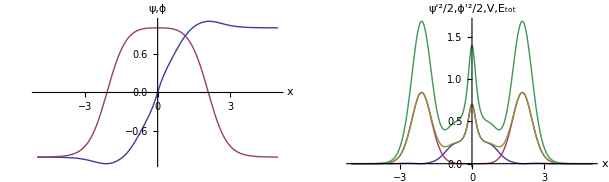

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

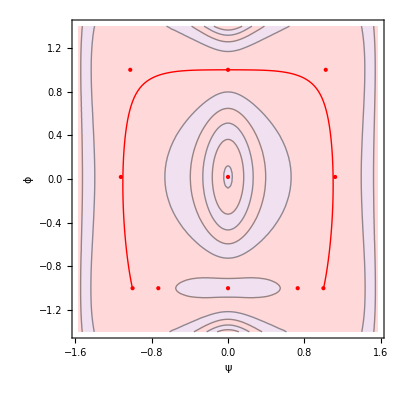

```mathematica
ChoixDeConditionsAuxLimites[3,8,2];
inf=5.0;
(* IntegrationEDpos1[xmin, xmax, valeur initiale de psi' à xmax, valeur initiale de phi' à xmax]; *)
IntegrationEDpos1[0.0,inf,-0.00001,-0.00001];
(* IntegrationEDneg1[-inf,0.0,0.00001,-0.00001];*)
IntEnergyDensity;
Resultats;
```

#### Passage au vrai vide avec ThetaM[k_,xi_]:=tm (1-Tanh[k xi])/2;

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

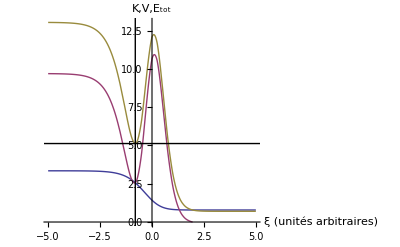

Énergie totale en fonction de x et t 
où ϕ(x,t) est ϕ(x) écrasée par le facteur ThetaM[k,xi] où tm = 1.5 par défault:

ψ(x,t)= ψ(x)

ϕ(x,t)= ThetaM[k,xi]  (ϕ(x)-ϕ(-∞))  +  ϕ(-∞)

ψ'(x,t)= ψ'(x)

ϕ'(x,t)= ThetaM[k,xi]  ϕ'(x)

-Graphics-

```mathematica
tinum=40; (* nombre des points sur graphique *)
tm=1.2;    (* facteur de magnification de phi de tm à 0 *)
xiinf=5.0;   (*  xi est entre ximinf  et +xiinf *)
ximinf=-5.0;   (*  xi est entre ximinf  et +xiinf *)
ThetaM[k_,xi_]:=tm(1-Tanh[k xi])/2;
k2=1;            (* valeur de k *)
PassageAuVraiVidePourphi
```

#### Calcul de l’action avec ThetaM[k_,xi_]:=tm (1-Tanh[k xi])/2;

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {-415.333} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-37.7575} lies outside the range of data in the interpolating function. Extrapolation will be used.

Action intégrée entre les points:
ξ_0 (minimum)= -0.804719  compression = 1.
ξ_1 (bounce)= 0.788563  compression = 0.205444
Action : 12.7028

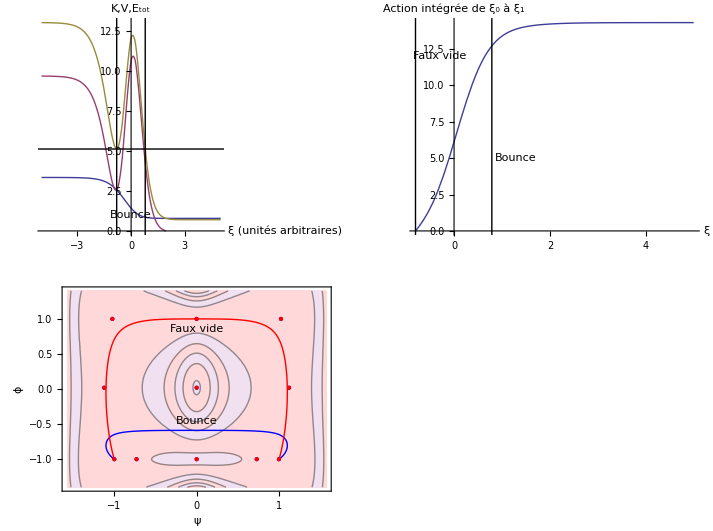

```mathematica
(* Calculs de M :
k2 =1, t -> xi(t) où xi(t) est dynamique
*)
tm=1.2;    (* facteur de magnification de phi de tm à 0 *)
xiinf=5.0;   (*  xi est entre ximinf  et +xiinf *)
ximinf=-5.0;   (*  xi est entre ximinf  et +xiinf *)
ThetaM[k_,xi_]:=tm(1-Tanh[k xi])/2;
k2=1;            (* valeur de k *)
t1sol=NSolve[ThetaM[k2,t1]==1,t1][[1]];
t2=1.0t1/.t1sol;

Action;
Print[GraphicsGrid[{{lp2,sep},{gvst}}]];
```

#### Passage au vrai vide avec ThetaM[k_,xi_]:=tm k (1-xi );

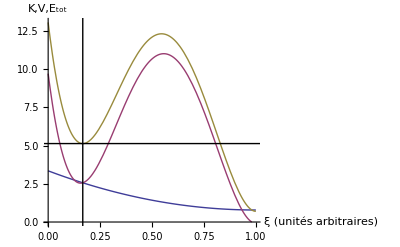

Énergie totale en fonction de x et t 
où ϕ(x,t) est ϕ(x) écrasée par le facteur ThetaM[k,xi] où tm = 1.5 par défault:

ψ(x,t)= ψ(x)

ϕ(x,t)= ThetaM[k,xi]  (ϕ(x)-ϕ(-∞))  +  ϕ(-∞)

ψ'(x,t)= ψ'(x)

ϕ'(x,t)= ThetaM[k,xi]  ϕ'(x)

-Graphics-

```mathematica
tinum=40; (* nombre des points sur graphique *)
tm=1.2;    (* facteur de magnification de phi de tm à 0 *)
xiinf=1;   (*  xi est entre ximinf  et +xiinf *)
ximinf=0;   (*  xi est entre ximinf  et +xiinf *)
ThetaM[k_,xi_]:=tm k (1-xi );
k2=1;            (* valeur de k *)
PassageAuVraiVidePourphi
```

#### Calcul de l’action avec ThetaM[k_,xi_]:=tm k (1-xi );

Action intégrée entre les points:
ξ_0 (minimum)= 0.166667  compression = 1.
ξ_1 (bounce)= 0.828746  compression = 0.205504
Action : 12.702

InterpolatingFunction::dmval: Input value {0.166684} lies outside the range of data in the interpolating function. Extrapolation will be used.

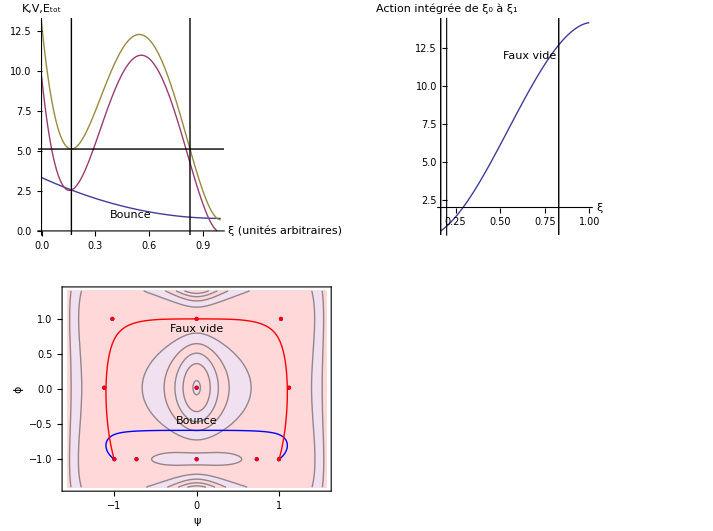

```mathematica
(* Calculs de M :
k2 =1, t -> xi(t) où xi(t) est dynamique
*)
tm=1.2;    (* facteur de magnification de phi de tm à 0 *)
xiinf=1;   (*  xi est entre ximinf  et +xiinf *)
ximinf=0;   (*  xi est entre ximinf  et +xiinf *)
ThetaM[k_,xi_]:=tm k (1-xi );
k2=1;            (* valeur de k *)
t1sol=NSolve[ThetaM[k2,t1]==1,t1][[1]];
t2=1.0t1/.t1sol;

Action;
Print[GraphicsGrid[{{lp2,sep},{gvst}}]];
```

```mathematica
(* Calculs de M :
k2 =1, t -> xi(t) où xi(t) est dynamique
*)
tm=1.2;    (* facteur de magnification de phi de tm à 0 *)
xiinf=5.0;   (*  xi est entre ximinf  et +xiinf *)
ximinf=-5.0;   (*  xi est entre ximinf  et +xiinf *)
ThetaM[k_,xi_]:=tm(1-Tanh[k xi])/2;
k2=1;            (* valeur de k *)
t1sol=NSolve[ThetaM[k2,t1]==1,t1][[1]];
t2=1.0t1/.t1sol;

Action;
Print[GraphicsGrid[{{lp2,sep},{gvst}}]];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-